# Symbolica Community Bridge: Demo Notebook

## Loading Symbolica Community Bridge

Access the paclet resources

```mathematica
Quit[]
```

```mathematica
PacletDirectoryLoad["/Users/vjhirsch/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/SymbolicaCommunityBridge"];
```

Load Symbolica Community Bridge

```mathematica
Needs["SCB`"] (* Use Quiet[Needs["SCB`"]] to mute welcome *)
```

Welcome::info: 

Symbolica Community Bridge:
---------------------

Requirements:

* Python3, with: 
    
    'python3 -m pip install pydot'
    'python3 -m pip install pyzmq'

* Symbolica community: (last tested with revision: c5507831b73e6f08dbc79dc0fcd41142fd14f9b4)
    
    'python3 -m pip install symbolica'
    
    or
    
    'git clone git@github.com:benruijl/symbolica-community.git && cd symbolica-community'
    'cargo run --features "python_stubgen"'
    'maturin build --release --features "python_stubgen"'
    'python3 -m pip install <path_to_the_wheel_generated_above>

* GammaLoop API:

    'git clone git@github.com:alphal00p/gammaloop.git && cd gammaloop'
    'maturin develop -m gammaloop-api/Cargo.toml --features=ufo_support,python_api'

* Then, initialize SymbolicaCommunityBridge with:

SCB`Init[
 PythonInterpreter -> ".../.venv/bin/python3", (* Or Automatic to rely on system defaults. *)                               
 GammaLoopPath -> ".../gammaloop_hedge_numerator/gammaloop-api/python", (* Or Null to disable gammaLoop features *)
 SymbolicaCommunityPath -> ".../.venv/lib/python3.12/site-packages", (* Or Null to disable symbolica community features *)
 SymbolicaLicense -> "YourSymbolicLicense" (* Optional *)
 FORMPath -> ".../bin/form", (* Or Null to disable symbolica FORM features *)
 DebugLevel -> Automatic (* Or any string default to pass as tracing directive *)
];

Initialized Symbolica Community Bridge

```mathematica
SCB`Init[
PythonInterpreter -> "/Users/vjhirsch/HEP_programs/symbolica-community_fork/.venv/bin/python3",
GammaLoopPath -> "/Users/vjhirsch/Documents/Work/gammaloop_hedge_numerator/gammaloop-api/python",
SymbolicaCommunityPath -> "/Users/vjhirsch/HEP_programs/symbolica-community_fork/.venv/lib/python3.12/site-packages",SymbolicaLicense -> "dcec4a5e#6a95649c#7dca8216-8afe-57c8-975e-03eb5e68e4ee",
FORMPath->"/Users/vjhirsch/HEP_programs/form/bin/form",
DebugLevel  -> Automatic
];
```

SCB`Info::info: Initializing SymbolicaCommunityBridge...

SCB`Info::info: Ignore deprecation warnings appearing below, if any

SCB`Info::info: SymbolicaCommunityBridge successfully initialized !

Reload it at any time, without resetting the initialization above (useful for debugging)

```mathematica
SCB`LoadSCB[];
```

SCB`Info::info: Reloading SymbolicaCommunityBridge function definitions...

Enumerate all functions available

```mathematica
Names["SCB`*"]//TableForm
```

SCB`Cmd
SCB`CurryExpr
SCB`ExprToString
SCB`GammaLoop
SCB`GammaLoopImportGraphs
SCB`Info
SCB`InfoMessage
SCB`Init
SCB`InitializedQ
SCB`LoadSCB
SCB`Pkg
SCB`Reset
SCB`ResetGammaLoop
SCB`RunPython
SCB`SimplifyColor
SCB`SimplifyGamma
SCB`StringToExpr
SCB`UncurryExpr
SCB`Welcome
SCB`WrappedExternalEvaluate
SCB`$GatedSymbols
SCB`$PublicSymbols
SCB`$ThisFile

Access usage info and options for any, e.g.

```mathematica
SCB`SimplifyColor::usage
Options[SCB`Init]//TableForm
```

SCB`SimplifyColor[expr] simplifies color algebra.

SCB`Private`PythonInterpreter→Automatic
SCB`Private`GammaLoopPath→Automatic
SCB`Private`GammaLoopStatePath→Automatic
SCB`Private`SymbolicaCommunityPath→Automatic
SCB`Private`FORMPath→Automatic
SCB`Private`SymbolicaLicense→Automatic
SCB`Private`DebugLevel→Automatic

## Symbolica core: Expand example

Test two-way parsing:

```mathematica
SCB`ExprToString[g[spenso`g][2][3,4][5],BackTickReplace->True]
SCB`StringToExpr[%,BackTickReplace->True]
```

g[spensoMATHEMATICABACKTICKg][2][3, 4][5]

g[spenso`g][2][3,4][5]

Use a Symbolica’s expand:

```mathematica
SCB`SExpand[(1.234`2*^-2*miaou`ϕ[μ][2][3]+1)^4]
```

1+0.0492 miaou`ϕ[μ][2][3]+0.00090774 (miaou`ϕ[μ][2][3])^2+7.44347×10^-6 (miaou`ϕ[μ][2][3])^3+2.28887×10^-8 (miaou`ϕ[μ][2][3])^4

You can set the debug level to one in order to monitor the python code executed by SymbolicaCommunityBridge

```mathematica
Expand[(miaou`ϕ[μ][2][3]+1)^4+1*^-24/(a+324.23434553`2)*<|aa->tt|>]
SCB`SetDebugLevel[1]
SCB`SExpand[(miaou`ϕ[μ][2][3]+1)^4+1*^-24/(a+324.23434553`2)*<|aa->tt|>]
SCB`SetDebugLevel[0]
```

<|aa→(1.×10^-24 tt)/(320.+a)+(1+miaou`ϕ[μ][2][3])^4|>

SCB`Info::info: Running the following Python code:

e = scb.to_symbolica(r'''Association[Rule[aa, Plus[Times[1.*^-24, Power[Plus[324., a], -1], tt], Power[Plus[1, miaouMATHEMATICABACKTICK\[Phi][\[Mu]][2][3]], 4]]]]''', debug=True)
e = e.expand()
scb.to_mathematica_form(e.to_mathematica())

Resulting string form of expression from Mathematica:

Association[Rule[aa, Plus[Times[1.*^-24, Power[Plus[324., a], -1], tt], Power[Plus[1, miaouMATHEMATICABACKTICK\[Phi][\[Mu]][2][3]], 4]]]]

Expression sent for parsing with Symboolica:

Association[Rule[aa, Plus[Times[1.e-24, Power[Plus[324., a], -1], tt], Power[Plus[1, miaou`\[Phi][\[Mu]][2][3]], 4]]]]

Resulting expression in symbolica:

python::{}::Association(python::{}::Rule(python::{}::aa,(1+miaou::{}::‖Phi‖(python::{}::‖Mu‖,‖,2,‖,3))^4+(324.000000000000+python::{}::a)^(-1)*1.00000000000000e-24*python::{}::tt))

<|aa→(1.×10^-24 tt)/(324.+a)+(1+miaou`ϕ[μ][2][3])^4|>

## Symbolica Community: Color and Lorentz algebra

Define a Lorentz object

```mathematica
GAMMA[i_,j_,μ_,OptionsPattern[{ dim->d}]]:=spenso`gamma[ spenso`bis[OptionValue[dim],i],spenso`bis[OptionValue[dim],j],spenso`mink[OptionValue[dim], μ]]
```

Use it!

```mathematica
SCB`SimplifyGamma[
GAMMA[1,2,mu] GAMMA[2,1,mu,dim->d]GAMMA[5,8,nu,dim->d]
]
```

d^2 spenso`gamma[spenso`bis[d,5],spenso`bis[d,8],spenso`mink[d,nu]]

Define color objects!

```mathematica
T[i_,j_,a_,OptionsPattern[{ nc->spenso`Nc}]]:=spenso`t[spenso`coad[OptionValue[nc]^2-1,a],spenso`cof[OptionValue[nc],i],spenso`dind[spenso`cof[OptionValue[nc],j]]]
```

```mathematica
f[a_,b_,c_,OptionsPattern[{ nc->spenso`Nc}]]:=spenso`f[spenso`coad[OptionValue[nc]^2-1,a],spenso`coad[OptionValue[nc]^2-1,b],spenso`coad[OptionValue[nc]^2-1,c]]
```

```mathematica
cid[a_,b_,OptionsPattern[{ nc->spenso`Nc}]]:=spenso`g[spenso`coad[OptionValue[nc]-1,a],spenso`coad[OptionValue[nc]-1,b]]
```

Use them!

```mathematica
SCB`SimplifyColor[
T[1,2,a]T[2,1,a]T[3,4,b]
]
```

(-1+Nc^2) spenso`TR spenso`t[spenso`coad[-1+Nc^2,b],spenso`cof[Nc,3],spenso`dind[spenso`cof[Nc,4]]]

Beware that squared f is currently bugged!

```mathematica
SCB`SimplifyColor[
f[1,2,3]f[1,2,3]
]
SCB`SimplifyColor[
f[1,2,3]f[1,3,2]
]
```

2 spenso`TR-6 (spenso`Nc)^2 spenso`TR+6 (spenso`Nc)^4 spenso`TR-2 (spenso`Nc)^6 spenso`TR-2 (-1+(spenso`Nc)^2) spenso`TR+(2 (-1+(spenso`Nc)^2) spenso`TR)/(spenso`Nc)-2 spenso`Nc (-1+(spenso`Nc)^2) spenso`TR+2 (spenso`Nc)^2 (-1+(spenso`Nc)^2) spenso`TR

-2 spenso`Nc (-1+(spenso`Nc)^2) spenso`TR

Complicated box of Adjoints!

```mathematica
RepeatedTiming[SCB`SimplifyColor[
f[1,2,5]f[2,3,6]f[3,4,7]f[4,1,8]f[9,10,5]f[10,11,6]f[11,12,7]f[12,9,8]
]]
```

{1.05287,24 (spenso`Nc)^2 (-1+(spenso`Nc)^2) (spenso`TR)^4+2 (spenso`Nc)^4 (-1+(spenso`Nc)^2) (spenso`TR)^4}

Specifying Nc helps speed a bit, but sadly some ouf our rules still yield parametric Nc.

```mathematica
RepeatedTiming[SCB`SimplifyColor[
f[1,2,5,nc->3]f[2,3,6,nc->3]f[3,4,7,nc->3]f[4,1,8,nc->3]f[9,10,5,nc->3]f[10,11,6,nc->3]f[11,12,7,nc->3]f[12,9,8,nc->3]
]]
```

{0.881415,192 (spenso`Nc)^2 (spenso`TR)^4+16 (spenso`Nc)^4 (spenso`TR)^4}

## GammaLoop steering

```mathematica
Quiet[SCB`LoadSCB[];]
```

After initialization with a GammaLoopPath supplied, the bridge allows to run commands, for example:

```mathematica
SCB`GammaLoop["display model"];
```

ModelNotLoaded

The gammaLoop handle appears as `gl` in Python, so it is also easy to call the gammaLoop API explicitly from Python, with e.g.:

```mathematica
SCB`RunPython["gl.run('display processes')"];
```

Processes:

```mathematica
SCB`GammaLoop["import model scalars-default.json"];
```

```mathematica
SCB`GammaLoop["save state -o"];
```

Saving state to /Users/vjhirsch/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/SymbolicaCommunityBridge/Examples/gammaloop_state..

The default gammaloop state loaded is in `./gammaloop_state` within the NotebookDirectory, but it also possible to reset the internal gammaloop engine to any pre-existing state:

```mathematica
SCB`ResetGammaLoop[GammaLoopStatePath->FileNameJoin[NotebookDirectory[],"gammaloop_state"]]
```

```mathematica
SCB`GammaLoop["display model"];
```

scalars

You can then run all the usual gammaloop CLI commands, such as importing the scalars model

```mathematica
vaccuumDotGraphs="
digraph vacuum_diag_A {

    num=\"1\";
    overall_factor=\"1\";

    edge [num=\"1\"];
    node [num=\"1\"];

    v0 -> v1 [particle=\"scalar_1\" lmb_id=0, id=0, num=\"Q(0,spenso::mink(4,11))\"];
    v1 -> v2 [particle=\"scalar_1\" id=1, num=\"Q(1,spenso::mink(4,11))\"];
    v2 -> v3 [particle=\"scalar_1\" id=2];
    v3 -> v0 [particle=\"scalar_1\" id=3];

}

digraph vacuum_diag_B {

    num=1;

    edge [num=\"1\"];
    node [num=\"1\"];

    v0 -> v1 [particle=\"scalar_1\" lmb_id=0, id=0, num=\"Q(0,spenso::mink(4,11))\"];
    v1 -> v2 [particle=\"scalar_1\" id=1, num=\"Q(1,spenso::mink(4,11))\"];
    v2 -> v3 [particle=\"scalar_1\" id=2, num=\"1\"];
    v3 -> v0 [particle=\"scalar_1\" id=3];

    // v10 -> v11 [particle=\"scalar_1\" lmb_id=1, id=4, num=\"Q(4,spenso::mink(4,12))\"];
    // v11 -> v12 [particle=\"scalar_1\" id=5, num=\"Q(5,spenso::mink(4,12))\"];
    // v12 -> v13 [particle=\"scalar_1\" id=6];
    // v13 -> v10 [particle=\"scalar_1\" id=7];
}
";
```

```mathematica
SCB`GammaLoopImportGraphs[vaccuumDotGraphs,"vacuum"];
```

```mathematica
SCB`GammaLoop["display processes"];
```

Processes:

#         0  vacuum

And capture the dot generated by gammaLoop

```mathematica
dotOutput=SCB`RunPython["gl.get_dot_files()"]
```

digraph vacuum_diag_A{
  num = "1";
  overall_factor = "1";
  projector = "1";
  v0[dod=0 num="1"];
  v1[dod=0 num="1"];
  v2[dod=0 num="1"];
  v3[dod=0 num="1"];

  v0:0	-> v1:1	 [id=0 dir=none source=0 sink=0  dod=-1 is_dummy=false lmb_id=0 lmb_rep="K(0,a___)" name=e0 num="Q(0,spenso::mink(4,11))" particle="scalar_1"];
  v1:2	-> v2:3	 [id=1 dir=none source=1 sink=0  dod=-1 is_dummy=false lmb_rep="K(0,a___)" name=e1 num="Q(1,spenso::mink(4,11))" particle="scalar_1"];
  v2:4	-> v3:5	 [id=2 dir=none source=1 sink=0  dod=-2 is_dummy=false lmb_rep="K(0,a___)" name=e2 num="1" particle="scalar_1"];
  v3:6	-> v0:7	 [id=3 dir=none source=1 sink=1  dod=-2 is_dummy=false lmb_rep="K(0,a___)" name=e3 num="1" particle="scalar_1"];
}

digraph vacuum_diag_B{
  num = "1";
  overall_factor = "1";
  projector = "1";
  v0[dod=0 num="1"];
  v1[dod=0 num="1"];
  v2[dod=0 num="1"];
  v3[dod=0 num="1"];

  v0:0	-> v1:1	 [id=0 dir=none source=0 sink=0  dod=-1 is_dummy=false lmb_id=0 lmb_rep="K(0,a___)" name=e0 num="Q(0,spenso::mink(4,11))" particle="scalar_1"];
  v1:2	-> v2:3	 [id=1 dir=none source=1 sink=0  dod=-1 is_dummy=false lmb_rep="K(0,a___)" name=e1 num="Q(1,spenso::mink(4,11))" particle="scalar_1"];
  v2:4	-> v3:5	 [id=2 dir=none source=1 sink=0  dod=-2 is_dummy=false lmb_rep="K(0,a___)" name=e2 num="1" particle="scalar_1"];
  v3:6	-> v0:7	 [id=3 dir=none source=1 sink=1  dod=-2 is_dummy=false lmb_rep="K(0,a___)" name=e3 num="1" particle="scalar_1"];
}

And load it within the dot parser of Mathematica, even though it is bad as it does not preserve all the attributes

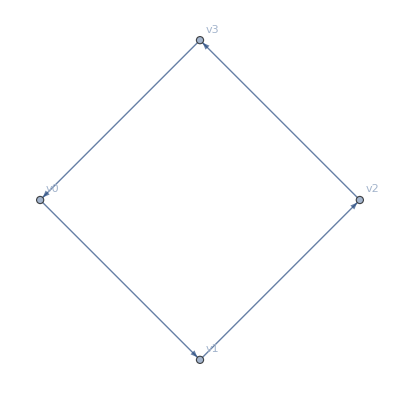

```mathematica
ImportString[dotOutput,"dot"]
```

Finally one can also load an existing dot file, requiring the SM model

```mathematica
SCB`GammaLoop["import model sm-default.json"];
```

[2025-11-07 18:09:39.202] @import::model        INFO    : Loading built-in JSON model sm-default

[2025-11-07 18:09:39.218] @gammalooprs::model   INFO    : The following [32m11[39m external parameters were forced to zero by the restriction card:

[34mlamWS, AWS, rhoWS, etaWS, ymc, yme, ymm, MC, Me, MM, WTau[39m

[2025-11-07 18:09:39.218] @gammalooprs::model   INFO    : The following [32m34[39m vertex rules were removed by the restriction card:

[34mV_82 -> (c~, d, G+) | V_83 -> (t~, d, G+) | V_84 -> (c~, s, G+) | V_85 -> (t~, s, G+) | V_86 -> (u~, b, G+) | V_87 -> (c~, b, G+) | V_90 -> (c~, d, W+) | V_91 -> (t~, d, W+) | V_92 -> (u~, s, W+) | V_94 -> (t~, s, W+) | V_95 -> (u~, b, W+) | V_96 -> (c~, b, W+) | V_101 -> (e+, e-, G0) | V_102 -> (mu+, mu-, G0) | V_104 -> (e+, e-, H) | V_105 -> (mu+, mu-, H) | V_110 -> (ve~, e-, G+) | V_111 -> (vm~, mu-, G+) | V_116 -> (b~, u, G-) | V_117 -> (d~, c, G-) | V_118 -> (s~, c, G-) | V_119 -> (b~, c, G-) | V_120 -> (d~, t, G-) | V_121 -> (s~, t, G-) | V_124 -> (s~, u, W-) | V_125 -> (b~, u, W-) | V_126 -> (d~, c, W-) | V_128 -> (b~, c, W-) | V_129 -> (d~, t, W-) | V_130 -> (s~, t, W-) | V_138 -> (c~, c, G0) | V_140 -> (c~, c, H) | V_145 -> (e+, ve, G-) | V_146 -> (mu+, vm, G-)[39m

[2025-11-07 18:09:39.218] @gammalooprs::model   INFO    : The following [32m36[39m couplings were removed by the restriction card:

[34mGC_13, GC_14, GC_16, GC_17, GC_18, GC_19, GC_20, GC_22, GC_23, GC_24, GC_25, GC_26, GC_28, GC_29, GC_42, GC_43, GC_44, GC_46, GC_47, GC_48, GC_84, GC_85, GC_86, GC_87, GC_88, GC_89, GC_90, GC_91, GC_92, GC_93, GC_101, GC_102, GC_103, GC_105, GC_106, GC_107[39m

And load this 6 photons hexagon loop graph:

```mathematica
SCB`GammaLoop["reset processes"];
```

[2025-11-07 18:21:23.101] @commands::reset      INFO    : All 1 processes have been cleared from the current state.

```mathematica
SCB`GammaLoop["set default-runtime kv integrator.n_start=1000 integrator.n_max=100000"]
```

```mathematica
SCB`GammaLoop["import graphs "<>FileNameJoin[NotebookDirectory[],"physical_1L_6photons.dot"]];
```

```mathematica
SCB`GammaLoop["display processes"];
```

Processes:

#         0  physical_1L_6photons

Now we can generate the 3D integrand code for it using Loop-Tree Duality

```mathematica
SCB`GammaLoop["generate"];
```

Set the kinematics of the process

```mathematica
SCB`GammaLoop["set process --process-id 0 kv kinematics.externals.data.momenta=[[500.0,0.0,-300.0,400.0],[500.0,0.0,300.0,-400.0],[88.55133305450298,-22.10069028768998,40.08035319168533,-75.80543095693663],[328.3294192270985,-103.8496118834563,-301.9337553895401,76.49492138716589],[152.3581094674306,-105.8809596665922,-97.7096383269757,49.54838522679282],[0,0,0,0]]"]
SCB`GammaLoop["set process --process-id 0 kv kinematics.externals.data.helicities=[1,1,1,1,1,1]"]
```

And do an evaluation! (currently bugged)

```mathematica
SCB`GammaLoop["inspect"]
```

[2025-11-07 18:24:07.979] @gammaloop_integra... INFO    : overlap structure of group 0: [2]

[31mThe application panicked (crashed).[0m

Message:  [36mindex out of bounds: the len is 0 but the index is 0[0m

Location: [35msrc/momentum_sample.rs[0m:[35m306[0m

Backtrace omitted. Run with RUST_BACKTRACE=1 environment variable to display it.

Run with RUST_BACKTRACE=full to include source snippets.

fatal runtime error: failed to initiate panic, error 5, aborting

/opt/local/Library/Frameworks/Python.framework/Versions/3.12/lib/python3.12/multiprocessing/resource_tracker.py:254: UserWarning: resource_tracker: There appear to be 1 leaked semaphore objects to clean up at shutdown

warnings.warn('resource_tracker: There appear to be %d '